```mathematica
G := 6.674*10^(-8)  (*en cgs*)
c := 2.998*10^(10)   (*en cgs*)
ti := 1.48*10^(12) (*s*)
ρt := 100 (*cgs *)
hbar := 1.05*10^(-27) (*cgs*)
```

```mathematica
ρcrit1[x_] := ((ρt +√(ρt^2 -4*(x^2*ρt)/((1+x^2)^3)))(1+x^2)^3)/(2*x^2)
```

```mathematica
ρcrit2[x_] := ((ρt -√(ρt^2 -4*(x^2*ρt)/((1+x^2)^3)))(1+x^2)^3)/(2*x^2)
```

```mathematica
func[x_]:= 1/2 √((3*c^2)/(8*π*G*ρcrit1[x]))(ArcSinh[x]+x*√(x^2+1))-ti
```

```mathematica
NSolve[func[x]==0, x]
```

$Aborted

```mathematica
γ := 0.2375
ρcrit = (√3 c^7)/(16*π^2*γ^3*G^2*hbar)
```

3.81074×10^114

```mathematica
fun[x_]:= 1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1))-ti
```

```mathematica
NSolve[fun[x]==0, x]
```

$Aborted

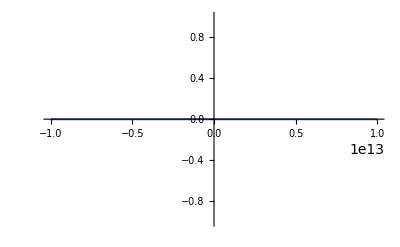

```mathematica
Plot[fun[x]+ti, {x, -10^13, 10^13}]
```

```mathematica
FindRoot[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1)), {x, 0}]
```

{x→0.}

```mathematica
Limit[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1)) -> ∞]
```

Limit::argtu: Limit called with 1 argument; 2 or 3 arguments are expected.

```mathematica
Limit[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1)) ,x->∞]
```

∞

```mathematica
Limit[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1)) ,x->-∞]
```

-∞

```mathematica
ver[x_]:=1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1))-ti 
ver[10^30]
```

1.02679×10^16

```mathematica
FindRoot[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1))-ti, {x, 10^30}, WorkingPrecision->50,AccuracyGoal->20,PrecisionGoal->20]
```

FindRoot::precw: The precision of the argument function (-1.48×10^12+1.02694×10^-44 (x √(1+x^2)+ArcSinh[x])) is less than WorkingPrecision (50.).

{x→1.2004903722253255843948491234674162692898767405791×10^28}

```mathematica
ver[1.200490372225325584394849123467416269289876740579126858498872439321`50.*^28]
```

0.

```mathematica
xi:=1.200490372225325584394849123467416269289876740579126858498872439321`50.*^28
```

```mathematica
ab := 1/(1+xi^2)^(1/2)
ab
```

8.329929361668428106822208579502042276443456113722×10^-29

```mathematica
ηb := √((8π G ab^2 ρcrit)/(3c^2))
ηb
```

4.05571×10^15